```mathematica
k[e_,u_]:=Sqrt[2*m*(u-e)/hbar^2]
```

```mathematica
κ[e_,u_]:= Sqrt[2*m*e/hbar^2]
```

```mathematica
k[e,u]
```

√2 √((m (-e+u))/hbar^2)

```mathematica
κ[e,u]
```

√2 √((e m)/hbar^2)

```mathematica
ψI[e_,u_,x_]:= aA*Exp[κ[e,u]*x]
```

```mathematica
ψIII[e_,u_,x_]:= gG*Exp[-κ[e,u]*x]
```

```mathematica
ψII[e_,u_,x_]:= cC*Exp[I*k[e,u]*x]+dD*Exp[-I*k[e,u]*x]
```

```mathematica
ψI[e,u,x]
```

aA ⅇ^(√2 √((e m)/hbar^2) x)

```mathematica
ψII[e,u,x]
```

dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x)+cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x)

```mathematica
ψIII[e,u,x]
```

ⅇ^(-√2 √((e m)/hbar^2) x) gG

```mathematica
D[ψI[e,u,x],x]
```

√2 aA ⅇ^(√2 √((e m)/hbar^2) x) √((e m)/hbar^2)

```mathematica
ψIp[e_,u_,x_]:=√2 aA ⅇ^(√2 √((e m)/hbar^2) x) √((e m)/hbar^2)
```

```mathematica
D[ψII[e,u,x],x]
```

-ⅈ √2 dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)

```mathematica
ψIIp[e_,u_,x_]:=-ⅈ √2 dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)
```

```mathematica
Solve[(ψIp[e,u,0]/ψI[e,u,0])-(ψIIp[e,u,0]/ψII[e,u,0])==0,dD]
```

{{dD→(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))}}

```mathematica
dD=(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))
```

(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))

```mathematica
D[ψIII[e,u,x],x]
```

-√2 ⅇ^(-√2 √((e m)/hbar^2) x) gG √((e m)/hbar^2)

```mathematica
ψIIIp[e_,u_,x_]:=-√2 ⅇ^(-√2 √((e m)/hbar^2) x) gG √((e m)/hbar^2)
```

```mathematica
lhs[e_,u_]:=ψIIIp[e,u,a]/ψIII[e,u,a]
```

```mathematica
lhs[e,u]
```

-√2 √((e m)/hbar^2)

```mathematica
ψIIp[e,u,a]/ψII[e,u,a]
```

(-ⅈ √2 dD ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2)) √((m (-e+u))/hbar^2))/(dD ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2))+cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2)))

```mathematica
Simplify[(-ⅈ √2 dD ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2)) √((m (-e+u))/hbar^2))/(dD ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2))+cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2)))]
```

(√2 (e (-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m-(-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m u+ⅈ (1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2)))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2)+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2)) (√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2))))

```mathematica
ExpToTrig[(√2 (e (-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m-(-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m u+ⅈ (1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2)))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2)+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2)) (√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2))))]
```

(√2 (-e m+m u+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2)+e m Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-m u Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ e m Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-ⅈ m u Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)+(√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)) (Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)])))

```mathematica
Simplify[(√2 (-e m+m u+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2)+e m Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-m u Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ e m Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-ⅈ m u Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)+(√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)) (Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)])))]
```

(√2 (hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+m (e-u) Sin[√2 a √((m (-e+u))/hbar^2)]))/(hbar^2 (√((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+√((e m)/hbar^2) Sin[√2 a √((m (-e+u))/hbar^2)]))

```mathematica
rhs[e_,u_]:=(√2 (hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+m (e-u) Sin[√2 a √((m (-e+u))/hbar^2)]))/(hbar^2 (√((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+√((e m)/hbar^2) Sin[√2 a √((m (-e+u))/hbar^2)]))
```

```mathematica
hbar = 197.32
```

197.32

```mathematica
m = 938.
```

938.

```mathematica
a = 1.0
```

1.

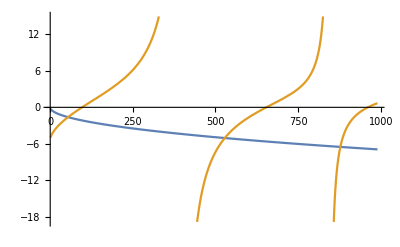

```mathematica
Plot[{lhs[e,1000],rhs[e,1000]},{e,1,990}]
```

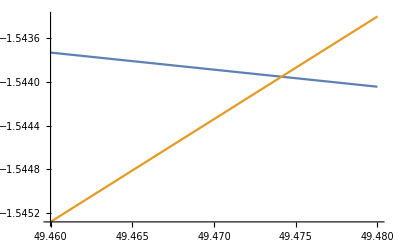

```mathematica
Plot[{lhs[e,100],rhs[e,100]},{e,49.46,49.48}]
```